```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<Utilities.m
```

```mathematica
(*Creating an XYList - loading a table of data while skipping the header.*)
data=Import[".\\Example data\\1. cavity transmission 1.txt","Table"][[2;;]];
```

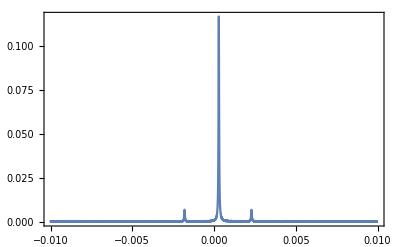

```mathematica
(*Plotting using defaultPlotFrameOptions*)
ListPlot[data,defaultPlotFrameOptions,PlotRange->Full,Axes->False, Joined->True]
```

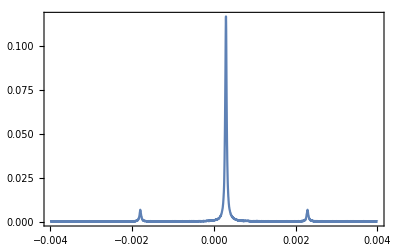

```mathematica
(*Plotting only a selected range*)
ListPlot[SelectRange[data,{-0.004,0.004}],defaultPlotFrameOptions,PlotRange->Full,Axes->False, Joined->True]
```

```mathematica
(*Peak finding*)
FindPeaksXY[data,1,0, 0.06]
```

{{0.00029427,0.11662688377599999}}

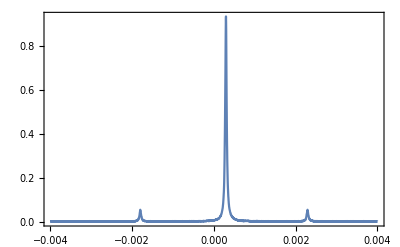

```mathematica
selData=SelectRange[data,{-0.004,0.004}];

(*Rescaling and adding an offset. This is illustrated using constnats, but the scale and the shift can be other XYLists*)
ListPlot[ScaleY[selData,8.],defaultPlotFrameOptions,PlotRange->Full,Axes->False, Joined->True]
```

```mathematica
(*Integration*)
IntegrateXY[data,{{-0.002, -0.0018}, {0.002, 0.0025}}]
```

7.14425×10^-7

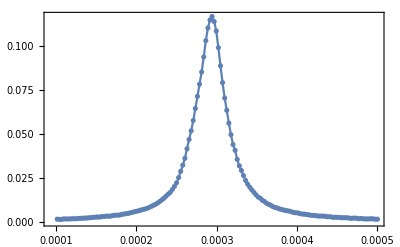

```mathematica
(*Note that Mathematica's ListPlot does not straightforwardly allow lotting the data points with the joing line. This can be done using ListPlotJ (and the analogous functions with the logarithmic axes)*)
ListPlotJ[SelectRange[data,{0.0001,0.0005}],defaultPlotFrameOptions,PlotRange->Full,Axes->False, Joined->True]
```

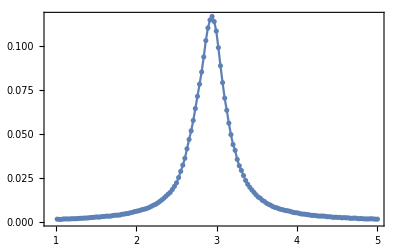

```mathematica
(*Re-scaling the data along X*)
ListPlotJ[SelectRange[ScaleX[data, 10^4],{1,5}],defaultPlotFrameOptions,PlotRange->Full,Axes->False, Joined->True]
```

```mathematica
(*Re-scaling the data along X*)
ListPlotJ[SelectRange[ScaleX[data, 10^4],{1,5}],defaultPlotFrameOptions,PlotRange->Full,Axes->False, Joined->True]
```